```mathematica
(*SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["FullHamiltonian.m",Path->FileNameJoin[{Directory[],"Packages"}]]*)

ϵ1=10;
ϵ2=5;
H=12;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
α=.529/a;(*Subscript[a, 0]/a, where Subscript[a, 0] is the Bohr radius*)
Ry=13.60569253;(*Rydberg unit of energy, in eV. 8πRy=e^2/(Subscript[a, 0] Subscript[ϵ, 0]) in eV*)
λ=6.328312923598453;(*electrons per unit cell*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
errorTrackingList={};

MM=8;
NN=4;
vals={};
vecs={};
degeneracies={};
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=20;
densityToNumStatesScaling=(NN(MM-1)N[Pi]/numPartitions)^-1;
λ = ((ϵ2/ϵ1)(1/2 ArcTan[(MM a)/(2H)]-1/2 ArcTan[-((MM-2) a)/(2H)])NN (MM-1) 1/numPartitions)^-1 numStates;

dk=N[Pi]/numPartitions;
initShift=0;
mm=Floor[(MM+1)/2];
totalCharge= -(ϵ2/ϵ1)(λ/N[π])(1/2 ArcTan[(MM a)/(2H)]-1/2 ArcTan[-((MM-2) a)/(2H)]);
chargeDist[x_,y_]:=Sin[(π y)/MM]Exp[-(2π x)/MM];
errorTolerance=.000000005;
EFermi= 0;

listvals=Flatten[Table[
 N[chargeDist[i ,j ]],
{i,1,NN},
{j,1,MM-1}
],1];
baseMatrix=BaseMatrixTakesChargeList[listvals];
{vals,vecs,degeneracies}=eigensystem[0];
```

```mathematica
(*first guess*)
(*tempList=Flatten[Table[
 N[chargeDist[i ,j ]],
{i,1,NN},
{j,1,MM-1}
],1];
tempTotal=tempList//Total;
listvals=Flatten[Table[
Abs[totalCharge/tempTotal]  N[ chargeDist[i ,j ]],
{i,1,NN},
{j,1,MM-1}
],1];*)
listvals={0.000053408317842178535,0.021108241880347663,1.2007636166776414,2.0961569923654184,1.2007641840133696,0.02110863766805081,0.000053613485353993856,4.3545898897087387*^-7,0.000025709503743037976,0.0019070497485204826,0.005244591614003893,0.0019070359488562861,0.000025664933118914545,3.1738798353898184*^-7,1.097933304344408*^-7,2.0923568613456498*^-7,7.228532114000308*^-7,1.5997059403308435*^-6,7.228470347828454*^-7,2.0921186169785314*^-7,1.096997893378022*^-7,5.000549054893499*^-8,9.239874134406486*^-8,1.2076724525507452*^-7,1.307949209635381*^-7,1.2076724438589444*^-7,9.239873746865891*^-8,5.000546954338203*^-8};



SelfConsistentDistribution[listvals,.05]
```

error=2.5293

error=0.743931

error=0.455666

error=0.441526

error=0.377536

error=0.347583

error=0.31061

error=0.281471

error=0.253515

error=0.228962

error=0.206535

error=0.186406

error=0.168198

error=0.151784

error=0.136965

error=0.123596

error=0.11153

error=0.100642

error=0.0908168

error=0.0819508

error=0.0739502

error=0.0667306

error=0.0602157

error=0.0543368

error=0.0490318

{{0.000018187,0.0124643,2.47716,4.49287,2.47716,0.0124644,0.0000182463,1.22818×10^-7,8.32247×10^-6,0.00096012,0.00257237,0.000960116,8.30968×10^-6,8.87964×10^-8,3.04557×10^-8,5.8096×10^-8,2.18736×10^-7,4.93175×10^-7,2.18734×10^-7,5.80894×10^-8,3.04296×10^-8,1.3871×10^-8,2.56304×10^-8,3.34999×10^-8,3.6282×10^-8,3.34999×10^-8,2.56304×10^-8,1.3871×10^-8},{2.5293,0.743931,0.455666,0.441526,0.377536,0.347583,0.31061,0.281471,0.253515,0.228962,0.206535,0.186406,0.168198,0.151784,0.136965,0.123596,0.11153,0.100642,0.0908168,0.0819508,0.0739502,0.0667306,0.0602157,0.0543368,0.0490318}}

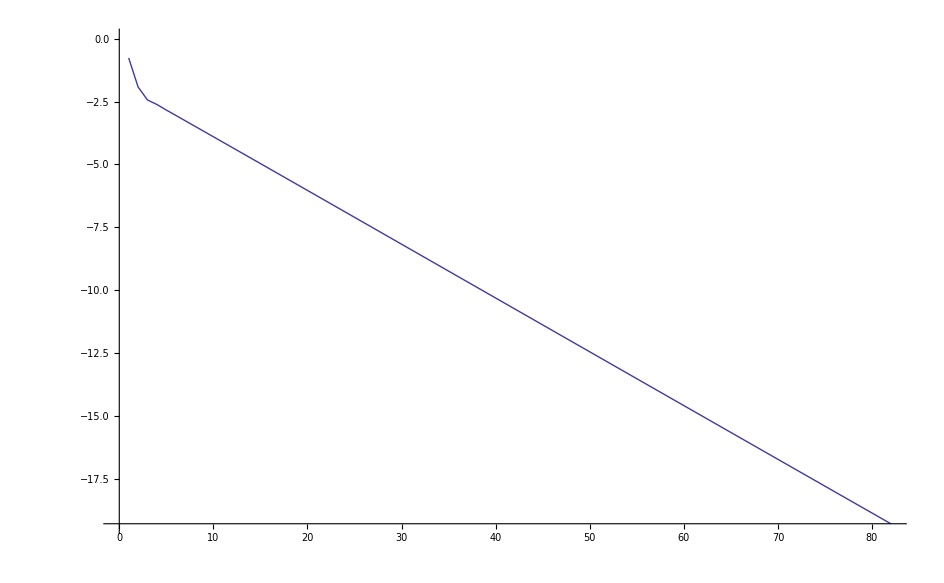

```mathematica
ListLinePlot[errorTrackingList//Log]
```

```mathematica
testList=normalizedSumList[numStates];
interpList=Flatten[Table[
{{i ,j} ,testList[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
testInterp = Interpolation[interpList,InterpolationOrder->1];
Print[Plot3D[testInterp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> {0,1.5}]]
interpList=Flatten[Table[
{{i ,j} ,listvals[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
testInterp = Interpolation[interpList,InterpolationOrder->1];
Print[Plot3D[testInterp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> {0,1.5}]]
interpList=Flatten[Table[
{{i ,j} ,-listvals[[j + (MM-1)(i-1)]]+testList[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
testInterp = Interpolation[interpList,InterpolationOrder->1];
Print[Plot3D[testInterp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> All]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

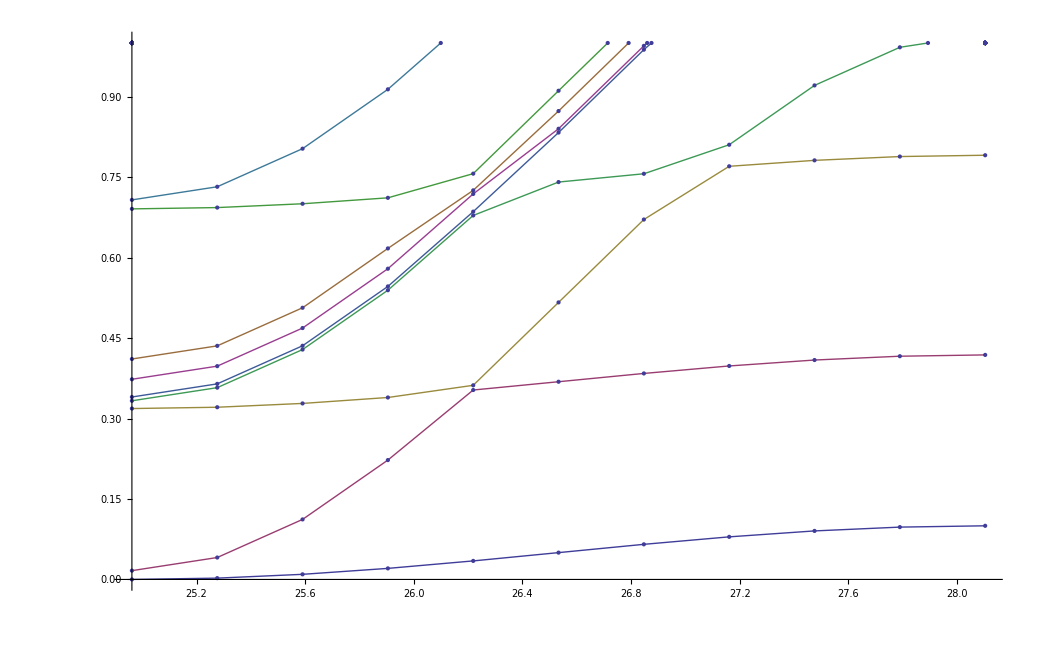

```mathematica
BandStructure[0,1]
```

```mathematica
dk
```

0.314159

```mathematica
vecs//MatrixForm
```

(0.00603188 | -1.71202×10^-17 | 4.51138×10^-17 | -0.0867951 | -3.42337×10^-17 | 5.56607×10^-17 | 0.502632 | -1.99493×10^-16 | 1.11661×10^-17 | -0.692485 | 8.17922×10^-16 | 3.94372×10^-18 | 0.502634 | -7.98515×10^-16 | -3.6655×10^-19 | -0.0867979 | -6.21248×10^-17 | -1.69412×10^-19 | 0.00604688 | -1.19723×10^-16 | 6.6993×10^-19 | -0.00023277 | 4.20128×10^-19 | 4.67187×10^-17 | 0.00046382 | -1.48078×10^-17 | -1.90573×10^-18 | -0.00303386 | 1.0159×10^-16 | 3.21823×10^-17 | 0.00512498 | 2.94903×10^-16 | 2.97555×10^-17 | -0.00303345 | -6.10623×10^-16 | -1.22793×10^-17 | 0.000456127 | -1.94289×10^-16 | 5.74619×10^-19 | -0.0000347474 | -4.44089×10^-16 | -4.517×10^-18 | 1.14142×10^-6 | -5.55112×10^-17 | -9.75242×10^-17 | -1.09209×10^-6 | 6.93889×10^-17 | 2.64419×10^-17 | 6.74607×10^-6 | -1.38778×10^-17 | 3.94141×10^-17 | -0.0000115601 | -1.21973×10^-16 | -2.39621×10^-19 | 6.74442×10^-6 | 1.96467×10^-18 | 1.64116×10^-18 | -1.05537×10^-6 | 1.24358×10^-16 | 4.45982×10^-19 | 8.75192×10^-8 | 5.54942×10^-17 | 4.03784×10^-20 | -2.69792×10^-9 | 1.19392×10^-16 | 4.60141×10^-18 | 1.62637×10^-9 | -1.22768×10^-17 | -1.39897×10^-18 | -9.40518×10^-9 | -1.46142×10^-17 | -1.47984×10^-18 | 1.60589×10^-8 | -1.09897×10^-16 | -2.07292×10^-20 | -9.4018×10^-9 | -1.70259×10^-18 | -5.5805×10^-20 | 1.54275×10^-9 | -3.55797×10^-17 | -4.03784×10^-20 | -1.36625×10^-10 | -5.48621×10^-17 | 5.38557×10^-29
0.00603188 | -6.50521×10^-18 | -2.09033×10^-17 | -0.0867951 | -6.88468×10^-18 | 9.56009×10^-17 | 0.502632 | -7.12971×10^-16 | 1.5527×10^-17 | -0.692485 | 2.43241×10^-16 | 8.6417×10^-18 | 0.502634 | -1.52656×10^-15 | -7.49029×10^-19 | -0.0867979 | 6.3274×10^-16 | -6.8017×10^-19 | 0.00604688 | 2.14238×10^-16 | -2.21596×10^-18 | -0.00023277 | 2.81893×10^-17 | 2.64628×10^-17 | 0.00046382 | -1.85114×10^-16 | 4.42346×10^-17 | -0.00303386 | -2.41777×10^-17 | -4.73642×10^-17 | 0.00512498 | -1.56125×10^-17 | 7.44885×10^-17 | -0.00303345 | 1.61329×10^-16 | -1.96379×10^-17 | 0.000456127 | 2.77556×10^-16 | 1.59716×10^-18 | -0.0000347474 | 5.55112×10^-17 | -1.81767×10^-18 | 1.14142×10^-6 | -1.38778×10^-16 | -4.35492×10^-17 | -1.09209×10^-6 | -4.16334×10^-17 | -2.79174×10^-17 | 6.74607×10^-6 | 9.02056×10^-17 | 2.5999×10^-17 | -0.0000115601 | -1.30104×10^-17 | -2.21016×10^-18 | 6.74442×10^-6 | -1.13322×10^-16 | 1.46617×10^-18 | -1.05537×10^-6 | -2.35248×10^-16 | 5.53206×10^-20 | 8.75192×10^-8 | -4.1612×10^-17 | 1.83314×10^-21 | -2.69792×10^-9 | 6.4934×10^-17 | 1.7912×10^-18 | 1.62637×10^-9 | -5.12099×10^-17 | 1.11454×10^-18 | -9.40518×10^-9 | 7.47634×10^-17 | -9.53523×10^-19 | 1.60589×10^-8 | -1.03299×10^-16 | 3.76552×10^-20 | -9.4018×10^-9 | 5.19852×10^-17 | -4.23762×10^-20 | 1.54275×10^-9 | -9.54907×10^-18 | -1.83304×10^-21 | -1.36626×10^-10 | 8.003×10^-17 | 7.90648×10^-29
0.00603188 | -2.68552×10^-18 | -9.26329×10^-18 | -0.0867951 | 6.162×10^-17 | -1.55312×10^-16 | 0.502632 | -1.55626×10^-15 | -2.8648×10^-17 | -0.692485 | 3.19894×10^-15 | -3.21174×10^-18 | 0.502634 | 2.46622×10^-17 | 1.93152×10^-19 | -0.0867979 | 1.53701×10^-15 | 8.8752×10^-19 | 0.00604688 | -6.03278×10^-16 | 2.38565×10^-18 | -0.00023277 | 1.50569×10^-17 | 2.60442×10^-17 | 0.00046382 | -3.34402×10^-16 | 3.30996×10^-17 | -0.00303386 | 5.11256×10^-16 | -8.44849×10^-17 | 0.00512498 | -3.15367×10^-16 | -1.40923×10^-17 | -0.00303345 | -5.0307×10^-16 | 3.30796×10^-18 | 0.000456127 | -1.10328×10^-15 | -5.89345×10^-19 | -0.0000347474 | -2.22045×10^-16 | 6.28636×10^-19 | 1.14142×10^-6 | -5.55112×10^-17 | 8.32444×10^-18 | -1.09209×10^-6 | 1.94289×10^-16 | -9.21536×10^-17 | 6.74607×10^-6 | -4.71845×10^-16 | 1.32722×10^-17 | -0.0000115601 | 7.85776×10^-17 | 6.06555×10^-20 | 6.74442×10^-6 | 4.80548×10^-17 | 3.35876×10^-19 | -1.05537×10^-6 | -2.36253×10^-16 | -2.35758×10^-19 | 8.75192×10^-8 | 2.22034×10^-16 | -4.44496×10^-20 | -2.69792×10^-9 | -8.50511×10^-17 | -1.15744×10^-18 | 1.62637×10^-9 | 2.66154×10^-17 | 4.21518×10^-18 | -9.40518×10^-9 | -3.75969×10^-17 | -4.91648×10^-19 | 1.60589×10^-8 | 1.64423×10^-16 | 3.15668×10^-20 | -9.4018×10^-9 | -1.78573×10^-16 | -1.30637×10^-20 | 1.54275×10^-9 | -7.80815×10^-17 | 4.44494×10^-20 | -1.36625×10^-10 | -1.92532×10^-16 | 6.34599×10^-29
-0.00603188 | 2.25514×10^-17 | 1.12415×10^-17 | 0.0867951 | -1.14925×10^-17 | 5.45587×10^-17 | -0.502632 | 5.27356×10^-16 | 4.8223×10^-17 | 0.692485 | -1.63758×10^-15 | 1.25×10^-17 | -0.502634 | 9.15934×10^-16 | 4.05179×10^-18 | 0.0867979 | -6.07153×10^-18 | 6.14785×10^-19 | -0.00604688 | 6.72639×10^-16 | -4.85182×10^-18 | 0.00023277 | -6.59195×10^-17 | -1.21279×10^-16 | -0.00046382 | 4.68375×10^-17 | 3.7408×10^-18 | 0.00303386 | -8.76035×10^-17 | -3.99371×10^-17 | -0.00512498 | -6.55725×10^-16 | -5.44553×10^-17 | 0.00303345 | 5.55112×10^-17 | 1.48665×10^-17 | -0.000456127 | 2.22045×10^-16 | -4.01176×10^-19 | 0.0000347474 | 1.11022×10^-16 | -7.63595×10^-19 | -1.14142×10^-6 | 2.77556×10^-17 | -6.70488×10^-18 | 1.09209×10^-6 | -4.77049×10^-17 | 6.5585×10^-17 | -6.74607×10^-6 | -6.28837×10^-18 | -6.0117×10^-17 | 0.0000115601 | 4.89225×10^-17 | 7.46207×10^-18 | -6.74442×10^-6 | -2.56858×10^-16 | -1.7943×10^-18 | 1.05537×10^-6 | -8.0715×10^-21 | 2.73143×10^-19 | -8.75192×10^-8 | 7.63281×10^-17 | -1.21282×10^-19 | 2.69792×10^-9 | -8.56276×10^-17 | -2.61583×10^-18 | -1.62637×10^-9 | -1.27426×10^-18 | -6.23454×10^-19 | 9.40518×10^-9 | -7.7095×10^-17 | 2.16233×10^-18 | -1.60589×10^-8 | 2.47641×10^-16 | -1.53795×10^-19 | 9.4018×10^-9 | 3.85165×10^-17 | 6.80871×10^-20 | -1.54275×10^-9 | -1.0301×10^-17 | 1.21282×10^-19 | 1.36625×10^-10 | 3.24146×10^-17 | 3.75264×10^-30
-1.13353×10^-16 | -0.0000670804 | -1.38819×10^-16 | 1.47766×10^-15 | 0.00875483 | 7.03073×10^-17 | -6.96405×10^-15 | -0.396344 | -2.92255×10^-17 | 1.08371×10^-15 | 0.825058 | -1.5575×10^-17 | 5.98133×10^-15 | -0.396343 | -3.53424×10^-18 | -1.45348×10^-15 | 0.00875482 | -1.77538×10^-18 | 1.0674×10^-16 | -0.000067094 | -1.35949×10^-19 | -2.83248×10^-18 | 4.07529×10^-6 | -2.23284×10^-17 | -1.06421×10^-17 | -0.000454305 | -2.39561×10^-17 | 4.84621×10^-17 | 0.0235341 | 4.38353×10^-17 | -1.29355×10^-16 | -0.0619592 | 1.43833×10^-17 | 6.245×10^-17 | 0.0235341 | 8.54476×10^-18 | 6.10623×10^-16 | -0.000454304 | -1.60936×10^-19 | 1.38778×10^-16 | 3.84657×10^-6 | 6.39383×10^-18 | -5.55112×10^-17 | -1.09043×10^-7 | 1.34207×10^-16 | 3.05311×10^-16 | 0.0000104611 | -4.8111×10^-17 | -1.11022×10^-16 | -0.000519739 | -2.01999×10^-17 | 2.08166×10^-17 | 0.00140397 | -4.41219×10^-18 | 9.63002×10^-17 | -0.000519738 | -1.31121×10^-18 | -9.13682×10^-17 | 0.000010461 | -6.99146×10^-19 | -3.02203×10^-17 | -9.68971×10^-8 | 5.22778×10^-20 | -1.38778×10^-16 | 1.80896×10^-9 | -3.84129×10^-18 | 3.38541×10^-17 | -1.52539×10^-7 | 7.2506×10^-19 | -1.29952×10^-16 | 7.21328×10^-6 | 8.00446×10^-19 | 1.06275×10^-16 | -0.0000195535 | 9.31736×10^-20 | 2.07142×10^-16 | 7.21327×10^-6 | 3.79456×10^-20 | -8.29533×10^-17 | -1.52538×10^-7 | -5.22987×10^-20 | 2.03642×10^-16 | 1.51415×10^-9 | 0.
0.0118398 | -1.27611×10^-16 | 4.93626×10^-19 | -0.154746 | 4.51841×10^-17 | -1.45307×10^-18 | 0.689851 | -2.0808×10^-15 | 1.48611×10^-19 | -3.39627×10^-6 | 9.397×10^-15 | 7.81884×10^-20 | -0.689851 | -1.9907×10^-15 | 3.68832×10^-20 | 0.154753 | 3.7405×10^-17 | 1.60953×10^-20 | -0.0118694 | -5.29091×10^-17 | -3.64829×10^-20 | 0.00033858 | 8.29415×10^-18 | -1.09941×10^-18 | 0.00078675 | -4.88433×10^-17 | -6.18598×10^-19 | -0.00408417 | 1.02796×10^-17 | -1.46466×10^-19 | -4.83181×10^-8 | -7.74988×10^-16 | -5.65635×10^-19 | 0.00408516 | 3.43421×10^-17 | 1.50322×10^-19 | -0.000803468 | 1.34441×10^-17 | -8.00752×10^-21 | 0.0000681484 | 4.03865×10^-17 | -1.39399×10^-20 | -1.98618×10^-6 | 9.67108×10^-17 | -2.60361×10^-19 | -1.77186×10^-6 | 3.64292×10^-17 | -4.44047×10^-19 | 9.01084×10^-6 | -4.33681×10^-18 | -4.48323×10^-19 | 1.98037×10^-10 | 2.91261×10^-17 | 8.80037×10^-20 | -9.01476×10^-6 | -6.00318×10^-18 | -1.05395×10^-20 | 1.85112×10^-6 | -1.27895×10^-17 | 1.14027×10^-21 | -1.71817×10^-7 | -5.96313×10^-18 | -1.8333×10^-21 | 4.97023×10^-9 | -1.08627×10^-16 | -3.05631×10^-20 | 2.52122×10^-9 | -2.99254×10^-17 | 4.71764×10^-20 | -1.25012×10^-8 | 9.45129×10^-17 | 1.48852×10^-20 | -3.85903×10^-13 | 5.96555×10^-17 | -1.60299×10^-21 | 1.25091×10^-8 | 8.51058×10^-17 | 4.2667×10^-22 | -2.70103×10^-9 | -1.76513×10^-18 | 1.83343×10^-21 | 2.686×10^-10 | 5.37662×10^-17 | 0.
-6.16576×10^-16 | -0.0000670804 | -1.13356×10^-17 | 8.07709×10^-15 | 0.00875483 | -7.20395×10^-17 | -3.68715×10^-14 | -0.396344 | -1.61423×10^-17 | 1.5554×10^-15 | 0.825058 | 5.31833×10^-18 | 3.71198×10^-14 | -0.396343 | -8.78373×10^-19 | -7.95653×10^-15 | 0.00875482 | 2.5411×10^-19 | 6.02681×10^-16 | -0.000067094 | 1.00119×10^-18 | -1.45554×10^-17 | 4.07529×10^-6 | 7.48877×10^-17 | -4.10845×10^-17 | -0.000454305 | -1.61355×10^-18 | 2.16278×10^-16 | 0.0235341 | -1.18712×10^-16 | 1.19154×10^-16 | -0.0619592 | 7.58965×10^-17 | -9.02056×10^-17 | 0.0235341 | -2.17247×10^-17 | 6.38378×10^-16 | -0.000454304 | 9.35124×10^-19 | -5.55112×10^-17 | 3.84657×10^-6 | -1.64854×10^-18 | -1.11022×10^-16 | -1.09043×10^-7 | -4.11987×10^-17 | -2.77556×10^-17 | 0.0000104611 | -3.56276×10^-17 | 1.36486×10^-24 | -0.000519739 | 3.47244×10^-17 | 8.32667×10^-17 | 0.00140397 | -3.29072×10^-18 | -1.47027×10^-16 | -0.000519738 | 1.68729×10^-18 | -8.9669×10^-17 | 0.000010461 | 2.96462×10^-20 | -3.09978×10^-16 | -9.68971×10^-8 | 5.90276×10^-21 | -5.20418×10^-17 | 1.80896×10^-9 | 1.7731×10^-18 | 1.42542×10^-16 | -1.52539×10^-7 | 1.37728×10^-18 | -4.30651×10^-16 | 7.21328×10^-6 | -1.22142×10^-18 | -1.34132×10^-18 | -0.0000195535 | 6.94567×10^-20 | 2.92419×10^-16 | 7.21327×10^-6 | -4.89668×10^-20 | 2.31128×10^-16 | -1.52538×10^-7 | -5.87422×10^-21 | -1.15512×10^-16 | 1.51415×10^-9 | 0.
-0.00603188 | -2.1684×10^-18 | 5.10629×10^-17 | 0.0867951 | 2.76472×10^-17 | 1.18733×10^-16 | -0.502632 | -2.11636×10^-16 | 3.74452×10^-17 | 0.692485 | 2.63331×10^-15 | 8.88723×10^-18 | -0.502634 | -2.51882×10^-15 | 1.52928×10^-18 | 0.0867979 | -8.73867×10^-17 | 1.75544×10^-20 | -0.00604688 | 1.20563×10^-15 | 5.7279×10^-19 | 0.00023277 | -7.97973×10^-17 | 2.06552×10^-17 | -0.00046382 | -4.18942×10^-17 | 1.46322×10^-17 | 0.00303386 | 5.23886×10^-16 | 1.04182×10^-17 | -0.00512498 | -3.98986×10^-16 | -7.58737×10^-18 | 0.00303345 | 7.21645×10^-16 | -3.59967×10^-18 | -0.000456127 | 1.11022×10^-16 | 7.68459×10^-20 | 0.0000347474 | 7.53582×10^-25 | -4.61303×10^-18 | -1.14142×10^-6 | 3.46945×10^-16 | -1.00262×10^-16 | 1.09209×10^-6 | 1.73472×10^-16 | -2.20097×10^-17 | -6.74607×10^-6 | -1.64799×10^-16 | 3.20213×10^-17 | 0.0000115601 | -2.46944×10^-17 | 2.65221×10^-18 | -6.74442×10^-6 | 1.6114×10^-16 | 1.36565×10^-18 | 1.05537×10^-6 | -6.93642×10^-17 | 3.84593×10^-19 | -8.75192×10^-8 | -5.48172×10^-16 | -2.47827×10^-20 | 2.69792×10^-9 | -6.6117×10^-18 | 3.32607×10^-18 | -1.62637×10^-9 | 1.49177×10^-17 | 1.49467×10^-18 | 9.40518×10^-9 | -5.67458×10^-17 | -1.26122×10^-18 | -1.60589×10^-8 | 3.44809×10^-18 | -6.03694×10^-20 | 9.4018×10^-9 | 9.23766×10^-17 | -4.72315×10^-20 | -1.54275×10^-9 | 4.27895×10^-17 | 2.47826×10^-20 | 1.36626×10^-10 | 2.6179×10^-16 | -4.63748×10^-29
-0.0118398 | -3.52474×10^-16 | 9.19274×10^-19 | 0.154746 | -3.98329×10^-16 | 7.68435×10^-20 | -0.689851 | 1.94963×10^-14 | 1.75438×10^-19 | 3.39627×10^-6 | -3.81691×10^-14 | 3.05858×10^-20 | 0.689851 | 3.55315×10^-14 | 1.8622×10^-20 | -0.154753 | -1.03964×10^-15 | 7.77053×10^-21 | 0.0118694 | 7.78457×10^-17 | 2.14434×10^-20 | -0.00033858 | 1.24006×10^-16 | 2.40662×10^-19 | -0.00078675 | -2.44176×10^-16 | 3.87267×10^-19 | 0.00408417 | -1.44893×10^-15 | 2.91837×10^-19 | 4.83181×10^-8 | 2.95033×10^-15 | -4.73159×10^-19 | -0.00408516 | -2.35435×10^-15 | 3.79908×10^-20 | 0.000803468 | -2.00144×10^-16 | -4.1206×10^-21 | -0.0000681484 | -9.6494×10^-18 | 7.71966×10^-22 | 1.98618×10^-6 | 3.10082×10^-17 | 4.33698×10^-20 | 1.77186×10^-6 | 1.20455×10^-16 | 5.6332×10^-19 | -9.01084×10^-6 | -1.30104×10^-17 | -2.48269×10^-20 | -1.98037×10^-10 | -8.24807×10^-17 | 1.58819×10^-22 | 9.01476×10^-6 | -6.47463×10^-17 | -3.17844×10^-21 | -1.85112×10^-6 | 7.37436×10^-18 | 1.1229×10^-21 | 1.71817×10^-7 | 1.69136×10^-17 | 3.33173×10^-22 | -4.97023×10^-9 | -1.19846×10^-16 | 4.49159×10^-21 | -2.52122×10^-9 | 3.43777×10^-17 | -2.75671×10^-20 | 1.25012×10^-8 | -4.59087×10^-17 | 1.21802×10^-21 | 3.85886×10^-13 | 4.58883×10^-19 | 7.43816×10^-23 | -1.25091×10^-8 | 2.88522×10^-17 | 8.39524×10^-23 | 2.70103×10^-9 | -1.68975×10^-17 | -3.32856×10^-22 | -2.686×10^-10 | -3.356×10^-17 | 0.)

```mathematica
list=normalizedProjectedSumList[numStates,1];
table=Flatten[Table[
{{i ,j} ,list[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
interp=Interpolation[table,InterpolationOrder->1];
Plot3D[interp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> All]
list=normalizedProjectedSumList[numStates,2];
table=Flatten[Table[
{{i ,j} ,list[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
interp=Interpolation[table,InterpolationOrder->1];
Plot3D[interp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> All]
list=normalizedProjectedSumList[numStates,3];
table=Flatten[Table[
{{i ,j} ,list[[j + (MM-1)(i-1)]]},
{i,1,NN},
{j,1,MM-1}
],1];
interp=Interpolation[table,InterpolationOrder->1];
Plot3D[interp[x,y],{x,1,NN},{y,1,MM-1},PlotRange-> All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
-Graphics3D-yz
-Graphics3D-zx
```

```mathematica
-Graphics3D-xy
```

```mathematica
EFermi-2.75
```

0.0684116